```mathematica
(*Pauli matrices,not spin operators*){sx,sy,sz}=Map[SparseArray,PauliMatrix[{1,2,3}]];

(*Pauli ladder operators*)
sP=(sx+I sy)/2;
sM=(sx-I sy)/2;

sZ[n_,j_]:=KroneckerProduct@@Insert[ConstantArray[IdentityMatrix[2],n-1],sz,Mod[j,n,1]];

sPlus[n_,j_]:=KroneckerProduct@@Insert[ConstantArray[IdentityMatrix[2],n-1],sP,Mod[j,n,1]];

sMinus[n_,j_]:=KroneckerProduct@@Insert[ConstantArray[IdentityMatrix[2],n-1],sM,Mod[j,n,1]];

sX[n_,j_]:=sPlus[n,j]+sMinus[n,j];
sY[n_,j_]:=(sPlus[n,j]-sMinus[n,j])/I;

comm[a_,b_]:=a.b-b.a;

(*Pauli-string basis*)
singleBasis={IdentityMatrix[2],sx,sy,sz};

singleBasisSymbols={1&,Subsuperscript["σ",#,"x"]&,Subsuperscript["σ",#,"y"]&,Subsuperscript["σ",#,"z"]&};

basis[n_]:=Function[{mat},(1/2^n) Map[Tr[ConjugateTranspose[Apply[KroneckerProduct,singleBasis[[#]]]].mat]&,Tuples[Table[Range[1,4],{n}]]]];

names[indexList_List]:=Times@@MapIndexed[singleBasisSymbols[[#]][#2[[1]]]&,indexList];

basisNames[n_]:=names/@Tuples[Table[Range[1,4],{n}]];

pauliReduce[matrix_?MatrixQ]:=Module[{n=Log[2,Length[matrix]]},Simplify[Total[basis[n][matrix] basisNames[n]]]];
```

```mathematica
pauliReduce[sX[4,1].sX[4,1]]          (*1*)
pauliReduce[comm[sX[4,1],sX[4,2]]]   (*0*)
pauliReduce[comm[sX[4,1].sY[4,2],sZ[4,1]+sZ[4,2]]]   (*-2 I σ₁ʸ*)
```

1

0

2 ⅈ (σ_1^x σ_2^x-σ_1^y σ_2^y)

```mathematica
H=With[{n=6},Sum[ sX[n,j].sX[n,j+1]+g sZ[n,j],{j,1,n}]];

lambdaH=With[{n=6},Sum[sZ[n,j],{j,1,n}]];

A1=comm[H,lambdaH];
Simplify[pauliReduce[A1]]
```

-2 ⅈ (σ_2^y σ_3^x+σ_2^x σ_3^y+σ_3^y σ_4^x+σ_3^x σ_4^y+σ_4^y σ_5^x+σ_4^x σ_5^y+σ_5^y σ_6^x+σ_1^y (σ_2^x+σ_6^x)+σ_5^x σ_6^y+σ_1^x (σ_2^y+σ_6^y))

```mathematica
A2= comm[H,A1];
Simplify[pauliReduce[A2]]
```

8 (g σ_1^y σ_2^y+σ_2^z-g σ_2^x σ_3^x+g σ_2^y σ_3^y+σ_3^z-g σ_3^x σ_4^x+σ_2^x σ_3^z σ_4^x+g σ_3^y σ_4^y+σ_4^z-g σ_4^x σ_5^x+σ_3^x σ_4^z σ_5^x+g σ_4^y σ_5^y+σ_5^z-g σ_5^x σ_6^x+σ_4^x σ_5^z σ_6^x+σ_1^z (1+σ_2^x σ_6^x)+g σ_1^y σ_6^y+g σ_5^y σ_6^y+σ_6^z+σ_1^x (-g σ_2^x+σ_2^z σ_3^x-g σ_6^x+σ_5^x σ_6^z))

```mathematica
A3 = comm[H,A2];
Simplify[pauliReduce[A3]/.g->0]
```

-32 ⅈ (σ_2^y σ_3^x+σ_2^x σ_3^y+σ_3^y σ_4^x+σ_3^x σ_4^y+σ_4^y σ_5^x+σ_4^x σ_5^y+σ_5^y σ_6^x+σ_1^y (σ_2^x+σ_6^x)+σ_5^x σ_6^y+σ_1^x (σ_2^y+σ_6^y))

```mathematica
A1R = pauliReduce[A1*I*α]
```

2 α (σ_2^y σ_3^x+σ_2^x σ_3^y+σ_3^y σ_4^x+σ_3^x σ_4^y+σ_4^y σ_5^x+σ_4^x σ_5^y+σ_5^y σ_6^x+σ_1^y (σ_2^x+σ_6^x)+σ_5^x σ_6^y+σ_1^x (σ_2^y+σ_6^y))

```mathematica
pauliReduce[A3*I*α]
```

32 α (σ_2^y σ_3^x+g^2 σ_2^y σ_3^x+σ_2^x σ_3^y+g^2 σ_2^x σ_3^y+σ_3^y σ_4^x+g^2 σ_3^y σ_4^x-g σ_2^y σ_3^z σ_4^x+σ_3^x σ_4^y+g^2 σ_3^x σ_4^y-g σ_2^x σ_3^z σ_4^y+σ_4^y σ_5^x+g^2 σ_4^y σ_5^x-g σ_3^y σ_4^z σ_5^x+σ_4^x σ_5^y+g^2 σ_4^x σ_5^y-g σ_3^x σ_4^z σ_5^y-g σ_1^z σ_2^y σ_6^x+σ_5^y σ_6^x+g^2 σ_5^y σ_6^x-g σ_4^y σ_5^z σ_6^x-g σ_1^z σ_2^x σ_6^y+σ_5^x σ_6^y+g^2 σ_5^x σ_6^y-g σ_4^x σ_5^z σ_6^y+σ_1^y ((1+g^2) σ_2^x-g σ_2^z σ_3^x+σ_6^x+g^2 σ_6^x-g σ_5^x σ_6^z)+σ_1^x ((1+g^2) σ_2^y-g σ_2^z σ_3^y+σ_6^y+g^2 σ_6^y-g σ_5^y σ_6^z))

```mathematica
A4 = comm[H,A3];
Simplify[pauliReduce[A4]]
```

-128 (-2 g σ_1^y σ_2^y-g^3 σ_1^y σ_2^y-σ_2^z-g^2 σ_2^z+g σ_2^x σ_3^x+g^3 σ_2^x σ_3^x-2 g σ_2^y σ_3^y-g^3 σ_2^y σ_3^y+g^2 σ_1^y σ_2^z σ_3^y-σ_3^z-g^2 σ_3^z+g σ_3^x σ_4^x+g^3 σ_3^x σ_4^x-σ_2^x σ_3^z σ_4^x-2 g^2 σ_2^x σ_3^z σ_4^x-2 g σ_3^y σ_4^y-g^3 σ_3^y σ_4^y+g^2 σ_2^y σ_3^z σ_4^y-σ_4^z-g^2 σ_4^z+g σ_4^x σ_5^x+g^3 σ_4^x σ_5^x-σ_3^x σ_4^z σ_5^x-2 g^2 σ_3^x σ_4^z σ_5^x+g σ_2^x σ_3^z σ_4^z σ_5^x-2 g σ_4^y σ_5^y-g^3 σ_4^y σ_5^y+g^2 σ_3^y σ_4^z σ_5^y-σ_5^z-g^2 σ_5^z+g σ_5^x σ_6^x+g^3 σ_5^x σ_6^x-σ_4^x σ_5^z σ_6^x-2 g^2 σ_4^x σ_5^z σ_6^x+g σ_3^x σ_4^z σ_5^z σ_6^x-2 g σ_1^y σ_6^y-g^3 σ_1^y σ_6^y-2 g σ_5^y σ_6^y-g^3 σ_5^y σ_6^y+g^2 σ_4^y σ_5^z σ_6^y-σ_6^z-g^2 σ_6^z+g^2 σ_1^y σ_5^y σ_6^z+σ_1^x ((g+g^3) σ_2^x-σ_2^z ((1+2 g^2) σ_3^x-g σ_3^z σ_4^x)+g σ_6^x+g^3 σ_6^x-σ_5^x σ_6^z-2 g^2 σ_5^x σ_6^z+g σ_4^x σ_5^z σ_6^z)+σ_1^z (-1-g^2+g σ_2^z σ_3^x σ_6^x+g^2 σ_2^y σ_6^y-σ_2^x ((1+2 g^2) σ_6^x-g σ_5^x σ_6^z)))

```mathematica
A5= comm[H,A4];
Simplify[pauliReduce[A5]/.g->0]
```

-512 ⅈ (σ_2^y σ_3^x+σ_2^x σ_3^y+σ_3^y σ_4^x+σ_3^x σ_4^y+σ_4^y σ_5^x+σ_4^x σ_5^y+σ_5^y σ_6^x+σ_1^y (σ_2^x+σ_6^x)+σ_5^x σ_6^y+σ_1^x (σ_2^y+σ_6^y))

```mathematica
A5R = pauliReduce[A5*I*α]/.g->1
```

512 α (5 σ_2^y σ_3^x+5 σ_2^x σ_3^y+5 σ_3^y σ_4^x-4 σ_2^y σ_3^z σ_4^x+5 σ_3^x σ_4^y-4 σ_2^x σ_3^z σ_4^y+5 σ_4^y σ_5^x-4 σ_3^y σ_4^z σ_5^x+σ_2^y σ_3^z σ_4^z σ_5^x+5 σ_4^x σ_5^y-4 σ_3^x σ_4^z σ_5^y+σ_2^x σ_3^z σ_4^z σ_5^y-4 σ_1^z σ_2^y σ_6^x+σ_1^z σ_2^z σ_3^y σ_6^x+5 σ_5^y σ_6^x-4 σ_4^y σ_5^z σ_6^x+σ_3^y σ_4^z σ_5^z σ_6^x-4 σ_1^z σ_2^x σ_6^y+σ_1^z σ_2^z σ_3^x σ_6^y+5 σ_5^x σ_6^y-4 σ_4^x σ_5^z σ_6^y+σ_3^x σ_4^z σ_5^z σ_6^y+σ_1^z σ_2^y σ_5^x σ_6^z+σ_1^z σ_2^x σ_5^y σ_6^z+σ_1^y (5 σ_2^x+σ_2^z (-4 σ_3^x+σ_3^z σ_4^x)+5 σ_6^x-4 σ_5^x σ_6^z+σ_4^x σ_5^z σ_6^z)+σ_1^x (5 σ_2^y+σ_2^z (-4 σ_3^y+σ_3^z σ_4^y)+5 σ_6^y-4 σ_5^y σ_6^z+σ_4^y σ_5^z σ_6^z))

```mathematica
P1 = (sX[6,0].sX[6,0]+sX[6,1])/2;
P2 = P1.(sX[6,0].sX[6,0]+sX[6,2])/2;
P3 = P2.(sX[6,0].sX[6,0]+sX[6,3])/2;
P4 = P3.(sX[6,0].sX[6,0]+sX[6,4])/2;
P1Z=(sX[6,0].sX[6,0]+sZ[6,1])/2;
P2Z = P1Z.(sX[6,0].sX[6,0]+sZ[6,2])/2;
P3Z = P2Z.(sX[6,0].sX[6,0]+sZ[6,3])/2;
P4Z = P3Z.(sX[6,0].sX[6,0]+sZ[6,4])/2;
```

```mathematica
Simplify[pauliReduce[comm[P1Z,A1*I]]]
Simplify[pauliReduce[comm[P2Z,A1*I]]/.g->0]
Simplify[pauliReduce[comm[P3Z,A1*I]]/.g->0]
Simplify[pauliReduce[comm[P4Z,A1*I]]/.g->0]
```

-2 ⅈ (σ_1^x (σ_2^x+σ_6^x)-σ_1^y (σ_2^y+σ_6^y))

-ⅈ ((1+σ_1^z) (σ_2^x σ_3^x-σ_2^y σ_3^y)+σ_1^x (2 σ_2^x+(1+σ_2^z) σ_6^x)-σ_1^y (2 σ_2^y+(1+σ_2^z) σ_6^y))

-1/2 ⅈ ((1+σ_1^z) (2 σ_2^x σ_3^x-2 σ_2^y σ_3^y+(1+σ_2^z) (σ_3^x σ_4^x-σ_3^y σ_4^y))+σ_1^x (1+σ_3^z) (2 σ_2^x+(1+σ_2^z) σ_6^x)-σ_1^y (1+σ_3^z) (2 σ_2^y+(1+σ_2^z) σ_6^y))

-1/4 ⅈ ((1+σ_1^z) (2 σ_2^x σ_3^x (1+σ_4^z)-2 σ_2^y σ_3^y (1+σ_4^z)+(1+σ_2^z) (2 σ_3^x σ_4^x-2 σ_3^y σ_4^y+(1+σ_3^z) (σ_4^x σ_5^x-σ_4^y σ_5^y)))+σ_1^x (1+σ_3^z) (1+σ_4^z) (2 σ_2^x+(1+σ_2^z) σ_6^x)-σ_1^y (1+σ_3^z) (1+σ_4^z) (2 σ_2^y+(1+σ_2^z) σ_6^y))

```mathematica
Simplify[pauliReduce[comm[P1Z,A3*I]]]
Simplify[pauliReduce[comm[P2Z,A3*I]]]
Simplify[pauliReduce[comm[P3Z,A3*I]]]
Simplify[pauliReduce[comm[P4Z,A3*I]]]
```

-32 ⅈ (σ_1^x ((1+g^2) σ_2^x-g σ_2^z σ_3^x+σ_6^x+g^2 σ_6^x-g σ_5^x σ_6^z)-σ_1^y ((1+g^2) σ_2^y-g σ_2^z σ_3^y+σ_6^y+g^2 σ_6^y-g σ_5^y σ_6^z))

-16 ⅈ ((1+σ_1^z) (σ_2^x ((1+g^2) σ_3^x-g (σ_3^z σ_4^x+σ_6^x))+σ_2^y (-((1+g^2) σ_3^y)+g (σ_3^z σ_4^y+σ_6^y)))+σ_1^x (2 (1+g^2) σ_2^x+(1+σ_2^z) (-g σ_3^x+(1+g^2) σ_6^x-g σ_5^x σ_6^z))-σ_1^y (2 (1+g^2) σ_2^y+(1+σ_2^z) (-g σ_3^y+(1+g^2) σ_6^y-g σ_5^y σ_6^z)))

-8 ⅈ ((1+σ_1^z) ((1+σ_2^z) (σ_3^x ((1+g^2) σ_4^x-g σ_4^z σ_5^x)-σ_3^y ((1+g^2) σ_4^y-g σ_4^z σ_5^y))+σ_2^x (2 (1+g^2) σ_3^x-g (1+σ_3^z) (σ_4^x+σ_6^x))+σ_2^y (-2 (1+g^2) σ_3^y+g (1+σ_3^z) (σ_4^y+σ_6^y)))+σ_1^x (2 (1+g^2) σ_2^x (1+σ_3^z)+(1+σ_2^z) (-2 g σ_3^x+(1+σ_3^z) ((1+g^2) σ_6^x-g σ_5^x σ_6^z)))-σ_1^y (2 (1+g^2) σ_2^y (1+σ_3^z)+(1+σ_2^z) (-2 g σ_3^y+(1+σ_3^z) ((1+g^2) σ_6^y-g σ_5^y σ_6^z))))

-4 ⅈ ((1+σ_1^z) (σ_2^x (2 (1+g^2) σ_3^x (1+σ_4^z)-g (1+σ_3^z) (2 σ_4^x+(1+σ_4^z) σ_6^x))+σ_2^y (-2 (1+g^2) σ_3^y (1+σ_4^z)+g (1+σ_3^z) (2 σ_4^y+(1+σ_4^z) σ_6^y))+(1+σ_2^z) (σ_3^x (2 (1+g^2) σ_4^x-g (1+σ_4^z) σ_5^x)+σ_3^y (-2 (1+g^2) σ_4^y+g (1+σ_4^z) σ_5^y)+(1+σ_3^z) (σ_4^x ((1+g^2) σ_5^x-g σ_5^z σ_6^x)-σ_4^y ((1+g^2) σ_5^y-g σ_5^z σ_6^y))))+σ_1^x (1+σ_4^z) (2 (1+g^2) σ_2^x (1+σ_3^z)+(1+σ_2^z) (-2 g σ_3^x+(1+σ_3^z) ((1+g^2) σ_6^x-g σ_5^x σ_6^z)))-σ_1^y (1+σ_4^z) (2 (1+g^2) σ_2^y (1+σ_3^z)+(1+σ_2^z) (-2 g σ_3^y+(1+σ_3^z) ((1+g^2) σ_6^y-g σ_5^y σ_6^z))))

```mathematica
Simplify[pauliReduce[comm[P1Z,A5*I]]/.g->0]
Simplify[pauliReduce[comm[P2Z,A5*I]]/.g->0]
Simplify[pauliReduce[comm[P3Z,A5*I]]/.g->0]
Simplify[pauliReduce[comm[P4Z,A5*I]]/.g->0]
```

-512 ⅈ (σ_1^x (σ_2^x+σ_6^x)-σ_1^y (σ_2^y+σ_6^y))

-256 ⅈ ((1+σ_1^z) (σ_2^x σ_3^x-σ_2^y σ_3^y)+σ_1^x (2 σ_2^x+(1+σ_2^z) σ_6^x)-σ_1^y (2 σ_2^y+(1+σ_2^z) σ_6^y))

-128 ⅈ ((1+σ_1^z) (2 σ_2^x σ_3^x-2 σ_2^y σ_3^y+(1+σ_2^z) (σ_3^x σ_4^x-σ_3^y σ_4^y))+σ_1^x (1+σ_3^z) (2 σ_2^x+(1+σ_2^z) σ_6^x)-σ_1^y (1+σ_3^z) (2 σ_2^y+(1+σ_2^z) σ_6^y))

-64 ⅈ ((1+σ_1^z) (2 σ_2^x σ_3^x (1+σ_4^z)-2 σ_2^y σ_3^y (1+σ_4^z)+(1+σ_2^z) (2 σ_3^x σ_4^x-2 σ_3^y σ_4^y+(1+σ_3^z) (σ_4^x σ_5^x-σ_4^y σ_5^y)))+σ_1^x (1+σ_3^z) (1+σ_4^z) (2 σ_2^x+(1+σ_2^z) σ_6^x)-σ_1^y (1+σ_3^z) (1+σ_4^z) (2 σ_2^y+(1+σ_2^z) σ_6^y))

```mathematica
Simplify[pauliReduce[comm[P3Z,A1*I]]]
Simplify[pauliReduce[comm[P3Z,A2*I]]]
Simplify[pauliReduce[comm[P3Z,A3*I]]]
Simplify[pauliReduce[comm[P3Z,A4*I]]]
Simplify[pauliReduce[comm[P3Z,A5*I]]]
```

-1/2 ⅈ ((1+σ_1^z) (2 σ_2^x σ_3^x-2 σ_2^y σ_3^y+(1+σ_2^z) (σ_3^x σ_4^x-σ_3^y σ_4^y))+σ_1^x (1+σ_3^z) (2 σ_2^x+(1+σ_2^z) σ_6^x)-σ_1^y (1+σ_3^z) (2 σ_2^y+(1+σ_2^z) σ_6^y))

2 ((1+σ_1^z) (2 g σ_2^x σ_3^y+(1+σ_2^z) (g σ_3^x σ_4^y+σ_3^y (g σ_4^x-σ_4^z σ_5^x))+σ_2^y (2 g σ_3^x-(1+σ_3^z) (σ_4^x+σ_6^x)))+σ_1^x (2 g σ_2^y (1+σ_3^z)-(1+σ_2^z) (σ_3^y-g (1+σ_3^z) σ_6^y))+σ_1^y (2 g σ_2^x (1+σ_3^z)-(1+σ_2^z) (σ_3^x-(1+σ_3^z) (g σ_6^x-σ_5^x σ_6^z))))

-8 ⅈ ((1+σ_1^z) ((1+σ_2^z) (σ_3^x ((1+g^2) σ_4^x-g σ_4^z σ_5^x)-σ_3^y ((1+g^2) σ_4^y-g σ_4^z σ_5^y))+σ_2^x (2 (1+g^2) σ_3^x-g (1+σ_3^z) (σ_4^x+σ_6^x))+σ_2^y (-2 (1+g^2) σ_3^y+g (1+σ_3^z) (σ_4^y+σ_6^y)))+σ_1^x (2 (1+g^2) σ_2^x (1+σ_3^z)+(1+σ_2^z) (-2 g σ_3^x+(1+σ_3^z) ((1+g^2) σ_6^x-g σ_5^x σ_6^z)))-σ_1^y (2 (1+g^2) σ_2^y (1+σ_3^z)+(1+σ_2^z) (-2 g σ_3^y+(1+σ_3^z) ((1+g^2) σ_6^y-g σ_5^y σ_6^z))))

32 ((1+σ_1^z) ((1+σ_2^z) (g σ_3^x ((2+g^2) σ_4^y-g σ_4^z σ_5^y)+σ_3^y ((g+g^3) σ_4^x+g σ_6^x-σ_4^z ((1+2 g^2) σ_5^x-g σ_5^z σ_6^x)))+g σ_2^x ((3+2 g^2) σ_3^y-g (1+σ_3^z) (σ_4^y+σ_6^y))+σ_2^y (g (3+2 g^2) σ_3^x-(1+σ_3^z) ((1+2 g^2) σ_4^x-g σ_4^z σ_5^x+σ_6^x+2 g^2 σ_6^x-g σ_5^x σ_6^z)))+σ_1^x (g (3+2 g^2) σ_2^y (1+σ_3^z)-(1+σ_2^z) ((1+3 g^2) σ_3^y-g (1+σ_3^z) ((2+g^2) σ_6^y-g σ_5^y σ_6^z)))+σ_1^y (g (3+2 g^2) σ_2^x (1+σ_3^z)-(1+σ_2^z) ((1+3 g^2) σ_3^x-(1+σ_3^z) ((g+g^3) σ_6^x-(1+2 g^2) σ_5^x σ_6^z+σ_4^x (g+g σ_5^z σ_6^z)))))

-128 ⅈ ((1+σ_1^z) ((1+σ_2^z) (σ_3^x ((1+3 g^2+g^4) σ_4^x+g (g σ_6^x+σ_4^z (-2 (1+g^2) σ_5^x+g σ_5^z σ_6^x)))-σ_3^y ((1+3 g^2+g^4) σ_4^y+g (g σ_6^y+σ_4^z (-2 (1+g^2) σ_5^y+g σ_5^z σ_6^y))))+σ_2^x (2 (1+3 g^2+g^4) σ_3^x-g (1+σ_3^z) (2 (1+g^2) σ_4^x-g σ_4^z σ_5^x+2 σ_6^x+2 g^2 σ_6^x-g σ_5^x σ_6^z))-σ_2^y (2 (1+3 g^2+g^4) σ_3^y-g (1+σ_3^z) (2 (1+g^2) σ_4^y-g σ_4^z σ_5^y+2 σ_6^y+2 g^2 σ_6^y-g σ_5^y σ_6^z)))+σ_1^x (2 (1+3 g^2+g^4) σ_2^x (1+σ_3^z)+(1+σ_2^z) (-4 (g+g^3) σ_3^x+(1+σ_3^z) ((1+3 g^2+g^4) σ_6^x-2 g (1+g^2) σ_5^x σ_6^z+g^2 σ_4^x (1+σ_5^z σ_6^z))))-σ_1^y (2 (1+3 g^2+g^4) σ_2^y (1+σ_3^z)+(1+σ_2^z) (-4 (g+g^3) σ_3^y+(1+σ_3^z) ((1+3 g^2+g^4) σ_6^y-2 g (1+g^2) σ_5^y σ_6^z+g^2 σ_4^y (1+σ_5^z σ_6^z)))))

16 ⅈ ((1+σ_1^x) σ_2^z (1+σ_3^x)+σ_1^z (1+σ_6^x+σ_2^x (1+σ_6^x)))

256 ⅈ (σ_2^z (1+σ_3^x+σ_1^x (1+σ_3^x))+σ_1^z (1+σ_6^x+σ_2^x (1+σ_6^x)))

1/4 ⅈ J ((1+σ_1^x) (2 σ_2^z (1+σ_3^x) (1+σ_4^x)+(1+σ_2^x) (2 σ_3^z (1+σ_4^x)+(1+σ_3^x) σ_4^z (1+σ_5^x)))+σ_1^z (1+σ_2^x) (1+σ_3^x) (1+σ_4^x) (1+σ_6^x))

64 ⅈ ((1+σ_1^x) (σ_2^z (2+2 σ_4^x+2 σ_3^x (1+σ_4^x))+(1+σ_2^x) (σ_3^z (2+2 σ_4^x)+(1+σ_3^x) σ_4^z (1+σ_5^x)))+σ_1^z (1+σ_4^x) (1+σ_3^x+σ_6^x+σ_3^x σ_6^x+σ_2^x (1+σ_3^x) (1+σ_6^x)))

```mathematica
pauliReduce[comm[P1,A1*I]]/.g->100
pauliReduce[comm[P2,A1*I]]/.g->100
pauliReduce[comm[P3,A1*I]]/.g->100
pauliReduce[comm[P4,A1*I]]/.g->100
```

2 ⅈ σ_1^z (σ_2^x+σ_6^x)

ⅈ ((1+σ_1^x) σ_2^z (1+σ_3^x)+σ_1^z (1+σ_2^x) (1+σ_6^x))

1/2 ⅈ ((1+σ_1^x) (2 σ_2^z (1+σ_3^x)+(1+σ_2^x) σ_3^z (1+σ_4^x))+σ_1^z (1+σ_2^x) (1+σ_3^x) (1+σ_6^x))

1/4 ⅈ ((1+σ_1^x) (2 σ_2^z (1+σ_3^x) (1+σ_4^x)+(1+σ_2^x) (2 σ_3^z (1+σ_4^x)+(1+σ_3^x) σ_4^z (1+σ_5^x)))+σ_1^z (1+σ_2^x) (1+σ_3^x) (1+σ_4^x) (1+σ_6^x))

```mathematica
Simplify[Asymptotic[pauliReduce[comm[P1,A3*I]],g->∞]]
Simplify[Asymptotic[pauliReduce[comm[P2,A3*I]],g->∞]]
Simplify[Asymptotic[pauliReduce[comm[P3,A3*I]],g->∞]]
Simplify[Asymptotic[pauliReduce[comm[P4,A3*I]],g->∞]]
```

32 ⅈ g^2 σ_1^z (σ_2^x+σ_6^x)

16 ⅈ g^2 ((1+σ_1^x) σ_2^z (1+σ_3^x)+σ_1^z (1+σ_2^x) (1+σ_6^x))

8 ⅈ g^2 ((1+σ_1^x) (2 σ_2^z (1+σ_3^x)+(1+σ_2^x) σ_3^z (1+σ_4^x))+σ_1^z (1+σ_2^x) (1+σ_3^x) (1+σ_6^x))

4 ⅈ g^2 ((1+σ_1^x) (2 σ_2^z (1+σ_3^x) (1+σ_4^x)+(1+σ_2^x) (2 σ_3^z (1+σ_4^x)+(1+σ_3^x) σ_4^z (1+σ_5^x)))+σ_1^z (1+σ_2^x) (1+σ_3^x) (1+σ_4^x) (1+σ_6^x))

```mathematica
Simplify[Asymptotic[pauliReduce[comm[P1,A1*I]],g->1]]
Simplify[Asymptotic[pauliReduce[comm[P2,A1*I]],g->1]]
Simplify[Asymptotic[pauliReduce[comm[P3,A1*I]],g->1]]
Simplify[Asymptotic[pauliReduce[comm[P4,A1*I]],g->1]]
```

2 ⅈ σ_1^z (σ_2^x+σ_6^x)

ⅈ ((1+σ_1^x) σ_2^z (1+σ_3^x)+σ_1^z (1+σ_2^x) (1+σ_6^x))

1/2 ⅈ ((1+σ_1^x) (2 σ_2^z (1+σ_3^x)+(1+σ_2^x) σ_3^z (1+σ_4^x))+σ_1^z (1+σ_2^x) (1+σ_3^x) (1+σ_6^x))

1/4 ⅈ ((1+σ_1^x) (2 σ_2^z (1+σ_3^x) (1+σ_4^x)+(1+σ_2^x) (2 σ_3^z (1+σ_4^x)+(1+σ_3^x) σ_4^z (1+σ_5^x)))+σ_1^z (1+σ_2^x) (1+σ_3^x) (1+σ_4^x) (1+σ_6^x))

```mathematica
Simplify[Asymptotic[pauliReduce[comm[P1,A3*I]],g->1]]
Simplify[Asymptotic[pauliReduce[comm[P2,A3*I]],g->1]]
Simplify[Asymptotic[pauliReduce[comm[P3,A3*I]],g->1]]
Simplify[Asymptotic[pauliReduce[comm[P4,A3*I]],g->1]]
```

32 ⅈ (σ_1^y (σ_2^y σ_6^x+σ_2^x σ_6^y)+σ_1^z (2 σ_2^x-σ_2^z σ_3^x+2 σ_6^x-σ_5^x σ_6^z))

16 ⅈ (σ_1^y σ_2^y σ_3^x+σ_2^y σ_3^y+σ_1^x σ_2^y σ_3^y+(1+σ_1^x) σ_2^z (2+2 σ_3^x-σ_3^z σ_4^x)+σ_1^y σ_2^y σ_6^x+σ_1^y σ_6^y+σ_1^y σ_2^x σ_6^y+σ_1^z (2+2 σ_6^x-σ_2^z (σ_3^x+σ_6^x)-σ_5^x σ_6^z+σ_2^x (2+2 σ_6^x-σ_5^x σ_6^z)))

8 ⅈ ((1+σ_1^x) (σ_2^y σ_3^y (1+σ_4^x)+σ_2^z (4+4 σ_3^x-σ_3^z (1+σ_4^x))+(1+σ_2^x) (σ_3^y σ_4^y+σ_3^z (2+2 σ_4^x-σ_4^z σ_5^x)))+σ_1^y (1+σ_3^x) (σ_2^y (1+σ_6^x)+(1+σ_2^x) σ_6^y)+σ_1^z (1+σ_3^x) (2+2 σ_6^x-σ_2^z (1+σ_6^x)-σ_5^x σ_6^z+σ_2^x (2+2 σ_6^x-σ_5^x σ_6^z)))

4 ⅈ ((1+σ_1^x) (2 σ_2^y σ_3^y (1+σ_4^x)+2 σ_2^z (2+2 σ_3^x-σ_3^z) (1+σ_4^x)+(1+σ_2^x) (σ_3^y σ_4^y (1+σ_5^x)+σ_3^z (4+4 σ_4^x-σ_4^z (1+σ_5^x))+(1+σ_3^x) (σ_4^y σ_5^y+σ_4^z (2+2 σ_5^x-σ_5^z σ_6^x))))+σ_1^y (1+σ_3^x) (1+σ_4^x) (σ_2^y (1+σ_6^x)+(1+σ_2^x) σ_6^y)+σ_1^z (1+σ_3^x) (1+σ_4^x) (2+2 σ_6^x-σ_2^z (1+σ_6^x)-σ_5^x σ_6^z+σ_2^x (2+2 σ_6^x-σ_5^x σ_6^z)))

```mathematica
Simplify[Asymptotic[pauliReduce[comm[P1,A5*I]],g->1]]
Simplify[Asymptotic[pauliReduce[comm[P2,A5*I]],g->1]]
Simplify[Asymptotic[pauliReduce[comm[P3,A5*I]],g->1]]
Simplify[Asymptotic[pauliReduce[comm[P4,A5*I]],g->1]]
```

-512 ⅈ (-σ_1^z (5 σ_2^x+σ_2^z (-4 σ_3^x+σ_3^z σ_4^x)+5 σ_6^x-4 σ_5^x σ_6^z+σ_4^x σ_5^z σ_6^z)+σ_1^y (σ_2^z (σ_3^y σ_6^x+σ_3^x σ_6^y)+σ_2^y (-4 σ_6^x+σ_5^x σ_6^z)+σ_2^x (-4 σ_6^y+σ_5^y σ_6^z)))

256 ⅈ (4 σ_1^y σ_2^y σ_3^x+4 σ_2^y σ_3^y+4 σ_1^x σ_2^y σ_3^y-σ_1^y σ_2^y σ_3^z σ_4^x-σ_2^y σ_3^z σ_4^y-σ_1^x σ_2^y σ_3^z σ_4^y+4 σ_1^y σ_2^y σ_6^x+4 σ_1^y σ_6^y+4 σ_1^y σ_2^x σ_6^y+σ_2^z (5-4 σ_3^z σ_4^x+σ_3^z σ_4^z σ_5^x+σ_1^x (5+5 σ_3^x+σ_3^z (-4 σ_4^x+σ_4^z σ_5^x))-σ_1^y σ_3^y σ_6^x+σ_3^x (5-σ_1^y σ_6^y))-σ_1^y σ_2^y σ_5^x σ_6^z-σ_1^y σ_5^y σ_6^z-σ_1^y σ_2^x σ_5^y σ_6^z+σ_1^z (5+5 σ_6^x-σ_2^y σ_3^y σ_6^x-σ_2^y σ_3^x σ_6^y-4 σ_5^x σ_6^z+σ_4^x σ_5^z σ_6^z+σ_2^z (-4 σ_3^x+σ_3^z σ_4^x-4 σ_6^x+σ_5^x σ_6^z)+σ_2^x (5+5 σ_6^x-4 σ_5^x σ_6^z+σ_4^x σ_5^z σ_6^z)))

128 ⅈ ((1+σ_1^x) (σ_2^y (-σ_3^z σ_4^y+σ_3^y (4+4 σ_4^x-σ_4^z σ_5^x))+σ_2^z (10+10 σ_3^x-σ_3^y σ_4^y+σ_3^z (-4-4 σ_4^x+σ_4^z σ_5^x))+(1+σ_2^x) (σ_3^y (4 σ_4^y-σ_4^z σ_5^y)+σ_3^z (5+5 σ_4^x+σ_4^z (-4 σ_5^x+σ_5^z σ_6^x))))+σ_1^y (-σ_2^z (σ_3^y (σ_4^x+σ_6^x)+(1+σ_3^x) σ_6^y)+(1+σ_2^x) (1+σ_3^x) (4 σ_6^y-σ_5^y σ_6^z)+σ_2^y (4+4 σ_6^x-σ_3^z (σ_4^x+σ_6^x)-σ_5^x σ_6^z+σ_3^x (4+4 σ_6^x-σ_5^x σ_6^z)))+σ_1^z (5+5 σ_3^x-σ_2^y σ_3^y σ_4^x+5 σ_6^x+5 σ_3^x σ_6^x-σ_2^y σ_3^y σ_6^x-σ_2^y σ_6^y-σ_2^y σ_3^x σ_6^y-4 σ_5^x σ_6^z-4 σ_3^x σ_5^x σ_6^z+σ_4^x σ_5^z σ_6^z+σ_3^x σ_4^x σ_5^z σ_6^z+σ_2^x (1+σ_3^x) (5+5 σ_6^x-4 σ_5^x σ_6^z+σ_4^x σ_5^z σ_6^z)+σ_2^z (-4-4 σ_6^x+σ_3^z (σ_4^x+σ_6^x)+σ_5^x σ_6^z+σ_3^x (-4-4 σ_6^x+σ_5^x σ_6^z))))

64 ⅈ (σ_1^y (1+σ_4^x) (-σ_2^z (σ_3^y (1+σ_6^x)+(1+σ_3^x) σ_6^y)+(1+σ_2^x) (1+σ_3^x) (4 σ_6^y-σ_5^y σ_6^z)+σ_2^y (4+4 σ_6^x-σ_3^z (1+σ_6^x)-σ_5^x σ_6^z+σ_3^x (4+4 σ_6^x-σ_5^x σ_6^z)))+σ_1^z (1+σ_4^x) (5+5 σ_3^x-σ_2^y σ_3^y+5 σ_6^x+5 σ_3^x σ_6^x-σ_2^y σ_3^y σ_6^x-σ_2^y σ_6^y-σ_2^y σ_3^x σ_6^y-4 σ_5^x σ_6^z-4 σ_3^x σ_5^x σ_6^z+σ_5^z σ_6^z+σ_3^x σ_5^z σ_6^z+σ_2^x (1+σ_3^x) (5+5 σ_6^x-4 σ_5^x σ_6^z+σ_5^z σ_6^z)+σ_2^z (-4-4 σ_6^x+σ_3^z (1+σ_6^x)+σ_5^x σ_6^z+σ_3^x (-4-4 σ_6^x+σ_5^x σ_6^z)))+(1+σ_1^x) (σ_2^y (-σ_3^z σ_4^y (1+σ_5^x)+σ_3^y (8+8 σ_4^x-σ_4^z (1+σ_5^x)))+σ_2^z (10+10 σ_4^x+10 σ_3^x (1+σ_4^x)-σ_3^y σ_4^y-σ_3^y σ_4^y σ_5^x+σ_3^z (-8-8 σ_4^x+σ_4^z (1+σ_5^x)))+(1+σ_2^x) (σ_3^y (-σ_4^z σ_5^y+σ_4^y (4+4 σ_5^x-σ_5^z σ_6^x))+σ_3^z (10+10 σ_4^x-σ_4^y σ_5^y+σ_4^z (-4-4 σ_5^x+σ_5^z σ_6^x))+(1+σ_3^x) (σ_4^y (4 σ_5^y-σ_5^z σ_6^y)+σ_4^z (5+5 σ_5^x+σ_5^z (-4 σ_6^x+σ_6^z))))))

```mathematica
Test =  Sin[k]/(( Cos[k]-h^2)^2+Sin[k]^2)
```

Sin[1]/((-h^2+Cos[1])^2+Sin[1]^2)

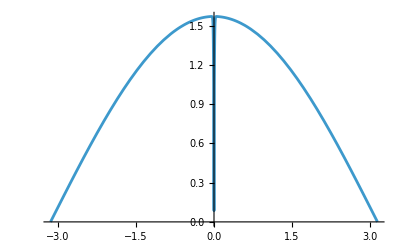

```mathematica
Plot[Abs[NIntegrate[Test/.k->ki,{h,1000,0}]],{ki,-Pi,Pi}]
```